# 2.4: Homoclinic bifurcation

```mathematica
b)
```

```mathematica
μ = 0.07
```

0.07

```mathematica
x =.
y=.
```

```mathematica
solb[x0_ , y0_] :=NDSolve[
{x'[t]==μ*x[t]+  y [t]-x[t]^2, 
y'[t] == -x[t]+μ*y[t]+2*x[t]^2 , x[0] == x0 , y[0] == y0} 
, {x,y} , {t,0,100}]
```

```mathematica
dz = 0.2
```

0.2

```mathematica
z = 1
```

1

```mathematica
initialC=Tuples[{Range[-z/2,z,dz],Range[-z/2,z,dz]}]
```

{{-0.5,-0.5},{-0.5,-0.3},{-0.5,-0.1},{-0.5,0.1},{-0.5,0.3},{-0.5,0.5},{-0.5,0.7},{-0.5,0.9},{-0.3,-0.5},{-0.3,-0.3},{-0.3,-0.1},{-0.3,0.1},{-0.3,0.3},{-0.3,0.5},{-0.3,0.7},{-0.3,0.9},{-0.1,-0.5},{-0.1,-0.3},{-0.1,-0.1},{-0.1,0.1},{-0.1,0.3},{-0.1,0.5},{-0.1,0.7},{-0.1,0.9},{0.1,-0.5},{0.1,-0.3},{0.1,-0.1},{0.1,0.1},{0.1,0.3},{0.1,0.5},{0.1,0.7},{0.1,0.9},{0.3,-0.5},{0.3,-0.3},{0.3,-0.1},{0.3,0.1},{0.3,0.3},{0.3,0.5},{0.3,0.7},{0.3,0.9},{0.5,-0.5},{0.5,-0.3},{0.5,-0.1},{0.5,0.1},{0.5,0.3},{0.5,0.5},{0.5,0.7},{0.5,0.9},{0.7,-0.5},{0.7,-0.3},{0.7,-0.1},{0.7,0.1},{0.7,0.3},{0.7,0.5},{0.7,0.7},{0.7,0.9},{0.9,-0.5},{0.9,-0.3},{0.9,-0.1},{0.9,0.1},{0.9,0.3},{0.9,0.5},{0.9,0.7},{0.9,0.9}}

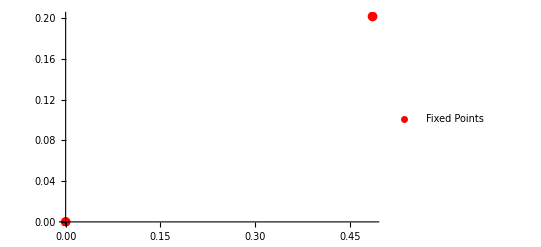

```mathematica
p1 = ListPlot[{{0,0}, { (1+μ^2)/(2+μ),(1-2 μ+μ^2-2 μ^3)/(2+μ)^2 }}, PlotMarkers->{Automatic,10}, PlotStyle -> {Red},PlotLegends->{"Fixed Points"} ]
```

```mathematica
{ (1+μ^2)/(2+μ),(1-2 μ+μ^2-2 μ^3)/(2+μ)^2 }
```

{0.485459,0.201688}

```mathematica
p4 = Show[ParametricPlot[
Evaluate[{x[t] , y[t]}/. solb[0.1, 0.1 ]]
,{t,0,100} , PlotRange->{{-0.4,0.6} , {-0.4,0.4}}]/. Line[x_] :> {Arrowheads[{0.05,0.0,0.0,0.0,0.0,0,0,0,0,0.05}], Arrow[x]}]
```

NDSolve::nderr: Error test failure at t == 62.5452; unable to continue.

-Graphics-

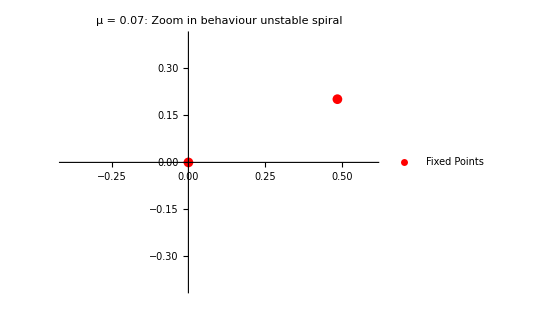

```mathematica
Show[p4,p1,PlotLabel-> "μ = 0.07: Zoom in behaviour unstable spiral"]
```

NDSolve::nderr: Error test failure at t == 26.1638; unable to continue.

NDSolve::nderr: Error test failure at t == 26.6047; unable to continue.

NDSolve::nderr: Error test failure at t == 27.0088; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

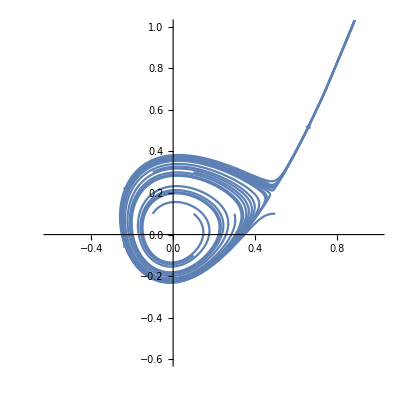

```mathematica
p2 = Show[
Table[
ParametricPlot[
Evaluate[{x[t] , y[t]}/. solb[initialC[[i,1]] , initialC[[i,2]]]]
,{t,0,30} , PlotRange->{{-0.6,1} , {-0.6,1}}],
{i,1,Length[initialC]}]/. Line[x_] :> {Arrowheads[{0.03,0.0,0.03}], Arrow[x]}
]
```

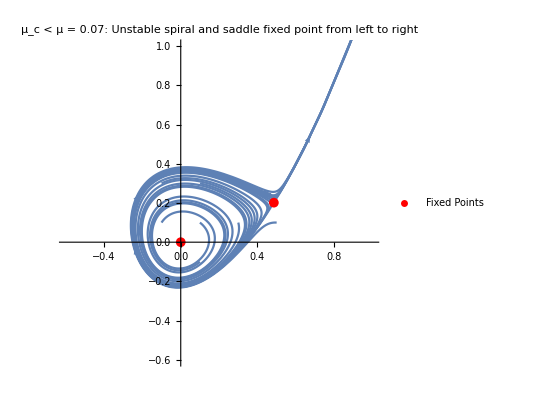

```mathematica
Show[p2,p1,PlotLabel-> "μ_c < μ = 0.07: Unstable spiral and  saddle fixed point from left to right"]
```

```mathematica
d)
```

We determine the saddle fixed point and it’s eigenvalues using linear stability analysis. We are interested in the eigenvalue of the unstable direction.

```mathematica
sol = Solve[{ μ*x+y-x^2==0, -x+μ*y+2*x^2 ==0 }, {x,y}]
```

{{x→0,y→0},{x→(1+μ^2)/(2+μ),y→(1-2 μ+μ^2-2 μ^3)/(2+μ)^2}}

```mathematica
a = sol[[2,1,2]]
```

(1+μ^2)/(2+μ)

```mathematica
b = sol[[2,2,2]]
```

(1-2 μ+μ^2-2 μ^3)/(2+μ)^2

```mathematica
A = {{μ-2*x, 1}, {-1+4*x, μ}}
```

{{-2 x+μ,1},{-1+4 x,μ}}

```mathematica
eigen = Eigensystem[A]
```

{{-x-√(-1+4 x+x^2)+μ,-x+√(-1+4 x+x^2)+μ},{{-(x+√(-1+4 x+x^2))/(-1+4 x),1},{-(x-√(-1+4 x+x^2))/(-1+4 x),1}}}

```mathematica
c = eigen[[1,1]]
```

-x-√(-1+4 x+x^2)+μ

```mathematica
d = eigen[[1,2]]
```

-x+√(-1+4 x+x^2)+μ

```mathematica
c = c/. x->a//Simplify
```

μ-1/(2+μ)-μ^2/(2+μ)-√((5+9 μ^2+4 μ^3+μ^4)/(2+μ)^2)

```mathematica
d = d/. x->a//Simplify
```

μ-1/(2+μ)-μ^2/(2+μ)+√((5+9 μ^2+4 μ^3+μ^4)/(2+μ)^2)

```mathematica
Plot[{c,d}, {μ, -1,1}, PlotLabels->{"c","d"}]
```

-Graphics-

So d>0 is the positive eigenvalue and thus the one belonging to the unstable direction.

```mathematica
e)
```

```mathematica
solb[x0_ , y0_] :=NDSolve[
{x'[t]==μ*x[t]+  y [t]-x[t]^2, 
y'[t] == -x[t]+μ*y[t]+2*x[t]^2 , x[0] == x0 , y[0] == y0} 
, {x,y} , {t,0,100}]
```

```mathematica
m = Range[20];
```

```mathematica
For[i = 1, i <=Length[m],i++,
m[[i]] =0.066-0.0005*i
]
```

```mathematica
m
```

{0.0655,0.065,0.0645,0.064,0.0635,0.063,0.0625,0.062,0.0615,0.061,0.0605,0.06,0.0595,0.059,0.0585,0.058,0.0575,0.057,0.0565,0.056}

```mathematica
Abs[m-0.066]
```

{0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01}

```mathematica
g = Range[Length[m]];
```

```mathematica
For[i=1,i<Length[m]+1,i++,
μ = m[[i]];

solb[x0_ , y0_] :=NDSolve[
{x'[t]==μ*x[t]+  y [t]-x[t]^2, 
y'[t] == -x[t]+μ*y[t]+2*x[t]^2 , x[0] == x0 , y[0] == y0} 
, {x,y} , {t,0,100}];
s = Evaluate[{x[t] , y[t]}/. solb[0,0.299]];
xx = s[[1,1]];
yy = s[[1,2]];

d = ((1+μ^2)/(2+μ)-xx)^2+((1-2 μ+μ^2-2 μ^3)/(2+μ)^2-yy)^2;
g[[i]] = Sqrt[Minimize[{d, 50<t<100},t][[1]]]
]
```

```mathematica
M = Abs[m-0.066]
```

{0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01}

```mathematica
data = Transpose@{Log[M],Log[g]}
```

{{-7.6009,-4.49904},{-6.90776,-4.05186},{-6.50229,-3.78051},{-6.21461,-3.58474},{-5.99146,-3.43122},{-5.80914,-3.30475},{-5.65499,-3.19707},{-5.52146,-3.10325},{-5.40368,-3.02005},{-5.29832,-2.87969},{-5.20301,-2.87722},{-5.116,-2.81484},{-5.03595,-2.7572},{-4.96185,-2.70359},{-4.89285,-2.65346},{-4.82831,-2.60635},{-4.76769,-2.56195},{-4.71053,-2.51988},{-4.65646,-2.47993},{-4.60517,-2.44187}}

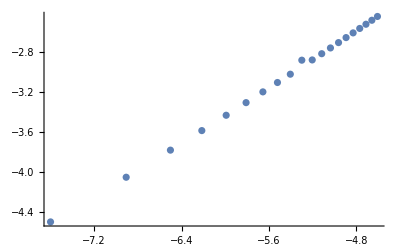

```mathematica
ListPlot[data]
```

```mathematica
line=Fit[data,{1,x},x]
```

0.740276+0.693584 x

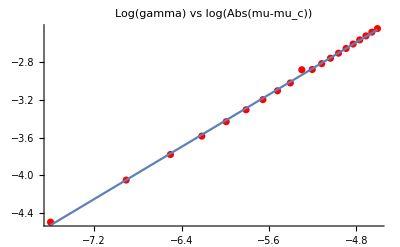

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[{line},{x,Min[Log[M]],Max[Log[M]]}], PlotLabel-> "Log(gamma) vs log(Abs(mu-mu_c))"]
```

So log(gamma) ~ 0.74+ 0.69 log(|mu-mu_c|) = 0.74+ log(|mu-mu_c|^0.69) so gamma ~ e^(0.74)*|mu-mu_c|^0.69 = 2.097 |mu-mu_c|^0.69, so A = 2.097 and a = 0.69 ≈ 0.7  in the scaling

```mathematica
f)
```

```mathematica
x =.
y =.
```

```mathematica
solu[mu_]:=NDSolve[
{x'[t]== mu* x[t]+y[t]-x[t]^2, 
y'[t] == -x[t]+mu *y[t]+2*x[t]^2, x[0] == 0, y[0] == 0.1} 
, {x,y} , {t,0,200}]
```

```mathematica
initialmu=Flatten[Tuples[{Range[0.01,0.065,0.001]}]]
ev = Table[solu[initialmu[[i]]][[1,1]], {i,1,Length[initialmu]}];
```

{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.065}

```mathematica
tab = Table[-FindArgMin[ev[[i,2]][t],{t,171,190}]+FindArgMin[ev[[i,2]][t],{t,179,186}], {i,1,Length[initialmu]}]
```

{{6.525},{6.55323},{6.58199},{13.2218},{13.2815},{6.67073},{6.70163},{6.73292},{6.7647},{6.79704},{6.82997},{6.86343},{6.8977},{13.8649},{13.9363},{7.00465},{7.04194},{7.08018},{7.11942},{7.15959},{7.2009},{7.24334},{14.5739},{7.33188},{7.37815},{7.42588},{7.47512},{7.52598},{7.57859},{7.6331},{7.68963},{7.74835},{7.80939},{7.873},{7.93938},{8.00881},{8.08153},{8.15797},{8.23848},{8.32348},{8.41356},{8.50942},{8.61178},{8.72162},{8.84015},{-2.99963×10^-6},{9.10973},{9.26528},{9.43897},{9.63563},{9.86242},{-1.81846×10^-6},{10.4572},{0.000018676},{11.4665},{12.4583}}

```mathematica
muu = initialmu
```

{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.065}

```mathematica
T = tab[[All,1]]
```

{6.525,6.55323,6.58199,13.2218,13.2815,6.67073,6.70163,6.73292,6.7647,6.79704,6.82997,6.86343,6.8977,13.8649,13.9363,7.00465,7.04194,7.08018,7.11942,7.15959,7.2009,7.24334,14.5739,7.33188,7.37815,7.42588,7.47512,7.52598,7.57859,7.6331,7.68963,7.74835,7.80939,7.873,7.93938,8.00881,8.08153,8.15797,8.23848,8.32348,8.41356,8.50942,8.61178,8.72162,8.84015,-2.99963×10^-6,9.10973,9.26528,9.43897,9.63563,9.86242,-1.81846×10^-6,10.4572,0.000018676,11.4665,12.4583}

Some periods have a very small value because something went wrong when looking for successive minima. This is solved by looking at the general trend of T vs log(abs(mu-mu_c)). This is not really necessary, but makes the plots later on better.

```mathematica
For[i=1,i<Length[T]+1,i++,
If[T[[i]]<5 || T[[i]]>13,T[[i]] = T[[1]]-1.46*(Log[Abs[muu[[i]]-0.066]]-Log[Abs[muu[[1]]-0.066]]),1]
]
```

```mathematica
data=Transpose@{Log[Abs[muu-0.066]],T}
```

{{-2.8824,6.525},{-2.90042,6.55323},{-2.91877,6.58199},{-2.93746,6.60539},{-2.95651,6.6332},{-2.97593,6.67073},{-2.99573,6.70163},{-3.01593,6.73292},{-3.03655,6.7647},{-3.05761,6.79704},{-3.07911,6.82997},{-3.10109,6.86343},{-3.12357,6.8977},{-3.14656,6.91066},{-3.17009,6.94502},{-3.19418,7.00465},{-3.21888,7.04194},{-3.24419,7.08018},{-3.27017,7.11942},{-3.29684,7.15959},{-3.32424,7.2009},{-3.35241,7.24334},{-3.38139,7.25353},{-3.41125,7.33188},{-3.44202,7.37815},{-3.47377,7.42588},{-3.50656,7.47512},{-3.54046,7.52598},{-3.57555,7.57859},{-3.61192,7.6331},{-3.64966,7.68963},{-3.68888,7.74835},{-3.7297,7.80939},{-3.77226,7.873},{-3.81671,7.93938},{-3.86323,8.00881},{-3.91202,8.08153},{-3.96332,8.15797},{-4.01738,8.23848},{-4.07454,8.32348},{-4.13517,8.41356},{-4.19971,8.50942},{-4.2687,8.61178},{-4.34281,8.72162},{-4.42285,8.84015},{-4.50986,8.90109},{-4.60517,9.10973},{-4.71053,9.26528},{-4.82831,9.43897},{-4.96185,9.63563},{-5.116,9.86242},{-5.29832,10.0522},{-5.52146,10.4572},{-5.80914,10.798},{-6.21461,11.4665},{-6.90776,12.4583}}

```mathematica
line=Fit[data,{1,x},x]
```

2.28976-1.47635 x

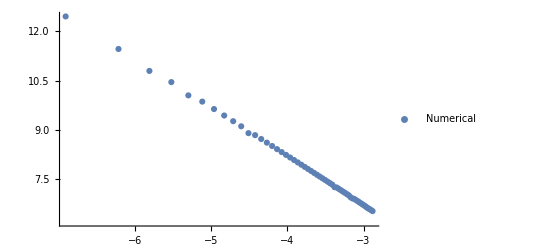

```mathematica
p1 = ListPlot[data, PlotLegends->{"Numerical"}]
```

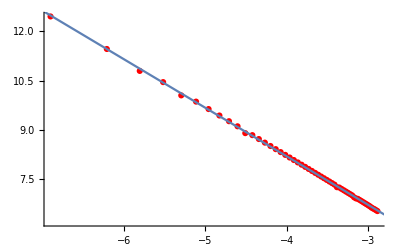

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[{line},{x,-9,-2}]]
```

Now all the period points roughly lie on the same trend line.

```mathematica
u = muu-1/(2+muu)-muu^2/(2+muu)+Sqrt[(5+9*muu^2+4*muu^3+muu^4)/(2+muu)^2]
```

{0.62501,0.625715,0.626421,0.627129,0.627838,0.628548,0.629259,0.629972,0.630686,0.631402,0.632119,0.632837,0.633557,0.634277,0.635,0.635723,0.636448,0.637174,0.637902,0.638631,0.639361,0.640093,0.640825,0.64156,0.642295,0.643032,0.64377,0.64451,0.645251,0.645993,0.646737,0.647482,0.648228,0.648976,0.649725,0.650475,0.651227,0.65198,0.652734,0.65349,0.654247,0.655005,0.655765,0.656526,0.657289,0.658052,0.658818,0.659584,0.660352,0.661121,0.661892,0.662663,0.663437,0.664211,0.664987,0.665764}

{{-2.8824,5.63261},{-2.90042,5.66082},{-2.91877,5.68959},{-2.93746,5.71893},{-2.95651,5.74888},{-2.97593,5.77946},{-2.99573,5.81069},{-3.01593,5.8426},{-3.03655,5.87521},{-3.05761,5.90857},{-3.07911,5.94269},{-3.10109,5.97763},{-3.12357,6.0134},{-3.14656,6.05006},{-3.17009,6.08765},{-3.19418,6.12621},{-3.21888,6.16579},{-3.24419,6.20644},{-3.27017,6.24823},{-3.29684,6.2912},{-3.32424,6.33544},{-3.35241,6.38102},{-3.38139,6.428},{-3.41125,6.47648},{-3.44202,6.52655},{-3.47377,6.57832},{-3.50656,6.6319},{-3.54046,6.68741},{-3.57555,6.74499},{-3.61192,6.8048},{-3.64966,6.867},{-3.68888,6.93179},{-3.7297,6.99938},{-3.77226,7.07001},{-3.81671,7.14396},{-3.86323,7.22154},{-3.91202,7.30311},{-3.96332,7.38908},{-4.01738,7.47994},{-4.07454,7.57625},{-4.13517,7.67868},{-4.19971,7.78802},{-4.2687,7.90525},{-4.34281,8.03154},{-4.42285,8.16836},{-4.50986,8.31755},{-4.60517,8.48149},{-4.71053,8.66332},{-4.82831,8.86729},{-4.96185,9.09934},{-5.116,9.36822},{-5.29832,9.68747},{-5.52146,10.0798},{-5.80914,10.5878},{-6.21461,11.3071},{-6.90776,12.5433}}

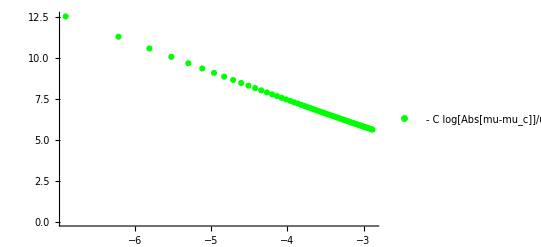

```mathematica
data3 = Transpose@{Log[Abs[muu-0.066]],-1.2*Log[0.95*Abs[muu-0.066]]/u}
p3 = ListPlot[data3, PlotStyle->{Green}, PlotLegends->{"- C log[Abs[mu-mu_c]]/u"}]
```

{{-2.8824,6.87751},{-2.90042,6.89798},{-2.91877,6.91891},{-2.93746,6.94032},{-2.95651,6.96221},{-2.97593,6.98462},{-2.99573,7.00756},{-3.01593,7.03106},{-3.03655,7.05514},{-3.05761,7.07982},{-3.07911,7.10513},{-3.10109,7.13111},{-3.12357,7.15777},{-3.14656,7.18515},{-3.17009,7.2133},{-3.19418,7.24223},{-3.21888,7.27201},{-3.24419,7.30266},{-3.27017,7.33424},{-3.29684,7.36679},{-3.32424,7.40037},{-3.35241,7.43504},{-3.38139,7.47087},{-3.41125,7.50792},{-3.44202,7.54627},{-3.47377,7.58601},{-3.50656,7.62723},{-3.54046,7.67002},{-3.57555,7.71451},{-3.61192,7.76082},{-3.64966,7.80908},{-3.68888,7.85946},{-3.7297,7.91213},{-3.77226,7.96728},{-3.81671,8.02514},{-3.86323,8.08597},{-3.91202,8.15006},{-3.96332,8.21775},{-4.01738,8.28943},{-4.07454,8.36556},{-4.13517,8.44669},{-4.19971,8.53347},{-4.2687,8.62669},{-4.34281,8.72731},{-4.42285,8.83653},{-4.50986,8.95585},{-4.60517,9.08722},{-4.71053,9.23321},{-4.82831,9.39727},{-4.96185,9.58427},{-5.116,9.80135},{-5.29832,10.0596},{-5.52146,10.3775},{-5.80914,10.7898},{-6.21461,11.3748},{-6.90776,12.3818}}

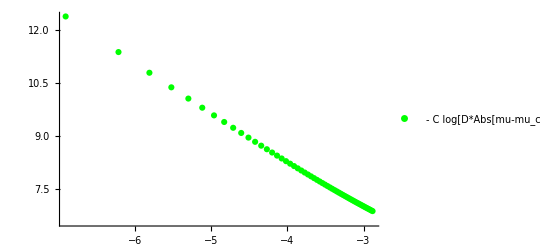

```mathematica
data3 = Transpose@{Log[Abs[muu-0.066]],-1.4*Log[0.349*Abs[muu-0.066]^0.7]/u}
p3 = ListPlot[data3, PlotStyle->{Green}, PlotLegends->{"- C log[D*Abs[mu-mu_c]^0.7]/u"}]
```

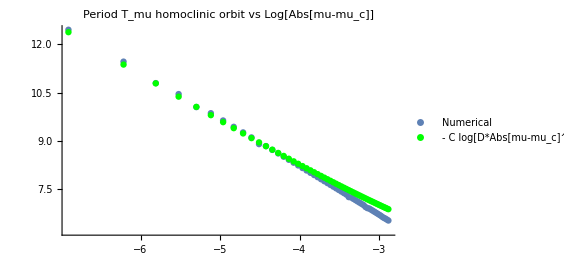

```mathematica
Show[p1,p3, PlotLabel->" Period T_mu homoclinic orbit vs Log[Abs[mu-mu_c]]"]
```

So we see that T_mu ~ - log([Abs(mu-mu_c)]) for mu close to mu_c. u scales as O(1) near mu_c so it won’t be important in the general scaling behaviour.
Remember that mu ~ mu_c means that -log([Abs(mu-mu_c)]) >>> 1, so that we only expect the curves to overlap at the left of the Figure. For mu further away from mu_c (so on the right of the figure), deviations are expected and we indeed see that the curves deviate away from each other in that region.